## Continuous data: enzyme example

We first read the data file “enzyme.dat”. Please note that 1mg/cc = 1 milligram / cubic centimetre  = 1 kg / m3.

```mathematica
SetDirectory[NotebookDirectory[]];
FileNames["*.dat"]
```

{bloodtype.dat,enzyme.dat,geyser.dat}

```mathematica
enzyme = Import["enzyme.dat"]
```

{{Enzyme,Concentration,(mg/cc)},{121},{25},{83},{110},{60},{101},{95},{81},{123},{67},{113},{78},{85},{145},{100},{70},{93},{118},{119},{57},{64},{151},{48},{92},{62},{104},{139},{201},{68},{95}}

```mathematica
Dimensions[enzyme]
```

{31}

We see the file contains 31 rows, with the first row containing 3 columns, and all other rows containing only 1 column. The first row is a list of 3 strings detailing the information contained in the data. We reformat the list as follows for convenience:

```mathematica
enzyme//TableForm
```

Enzyme Concentration(mg/cc)
121
25
83
110
60
101
95
81
123
67
113
78
85
145
100
70
93
118
119
57
64
151
48
92
62
104
139
201
68
95

```mathematica
enzyme[[2;;,All]]
```

{{121},{25},{83},{110},{60},{101},{95},{81},{123},{67},{113},{78},{85},{145},{100},{70},{93},{118},{119},{57},{64},{151},{48},{92},{62},{104},{139},{201},{68},{95}}

```mathematica
ef = Flatten[enzyme[[2;;,All]]]
```

{121,25,83,110,60,101,95,81,123,67,113,78,85,145,100,70,93,118,119,57,64,151,48,92,62,104,139,201,68,95}

```mathematica
enzyme =Join[{"Enzyme Concentration(mg/cc)"},ef]
```

{Enzyme Concentration(mg/cc),121,25,83,110,60,101,95,81,123,67,113,78,85,145,100,70,93,118,119,57,64,151,48,92,62,104,139,201,68,95}

```mathematica
Dimensions[enzyme]
```

{31}

We now start building the frequency table:

```mathematica
Min[enzyme[[2;;]]]
```

25

```mathematica
Max[enzyme[[2;;]]]
```

201

The following function creates bins of width 10, starting at Ceiling[Min[data]-dx,dx], and the last bin ending at Floor[Max[data]+dx,dx], and it counts how many samples fall within each bin:

```mathematica
enzyme
```

{Enzyme Concentration(mg/cc),121,25,83,110,60,101,95,81,123,67,113,78,85,145,100,70,93,118,119,57,64,151,48,92,62,104,139,201,68,95}

```mathematica
BinCounts[enzyme,10]
```

{1,0,1,1,5,2,3,4,3,4,2,1,1,1,0,0,0,0,1}

```mathematica
Total[BinCounts[enzyme,10]]
```

30

```mathematica
Ceiling[Min[enzyme[[2;;]]]-10,10]
```

20

```mathematica
Floor[Max[enzyme[[2;;]]]+10,10]
```

210

That means, the boundaries between the bins are as follows:

```mathematica
enzyme[[2;;]]
```

{121,25,83,110,60,101,95,81,123,67,113,78,85,145,100,70,93,118,119,57,64,151,48,92,62,104,139,201,68,95}

```mathematica
Ceiling[Min[enzyme[[2;;]]]-10,10]
```

20

```mathematica
enzyme[[2;;]]
```

{121,25,83,110,60,101,95,81,123,67,113,78,85,145,100,70,93,118,119,57,64,151,48,92,62,104,139,201,68,95}

```mathematica
Floor[Max[enzyme[[2;;]]]+10,10]
```

210

```mathematica
RR=Range[Ceiling[Min[enzyme[[2;;]]]-10,10], Floor[Max[enzyme[[2;;]]]+10,10],10]
```

{20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210}

```mathematica
Dimensions[RR]
```

{20}

```mathematica
{RR[[#]],RR[[#+1]]} &/@ Range[1,19]
```

{{20,30},{30,40},{40,50},{50,60},{60,70},{70,80},{80,90},{90,100},{100,110},{110,120},{120,130},{130,140},{140,150},{150,160},{160,170},{170,180},{180,190},{190,200},{200,210}}

```mathematica
{RR[[#]],RR[[#+1]],BinCounts[enzyme,10][[#]]} &/@ Range[1,19]
```

{{20,30,1},{30,40,0},{40,50,1},{50,60,1},{60,70,5},{70,80,2},{80,90,3},{90,100,4},{100,110,3},{110,120,4},{120,130,2},{130,140,1},{140,150,1},{150,160,1},{160,170,0},{170,180,0},{180,190,0},{190,200,0},{200,210,1}}

The following function lists the samples that fall within each of those bins:

```mathematica
enzyme[[2;;]]
```

{121,25,83,110,60,101,95,81,123,67,113,78,85,145,100,70,93,118,119,57,64,151,48,92,62,104,139,201,68,95}

```mathematica
BinLists[enzyme,10]
```

{{25},{},{48},{57},{60,67,64,62,68},{78,70},{83,81,85},{95,93,92,95},{101,100,104},{110,113,118,119},{121,123},{139},{145},{151},{},{},{},{},{201}}

We now calculate the relative frequency:

```mathematica
relfreez=N[BinCounts[enzyme,10]/30]
```

{0.0333333,0.,0.0333333,0.0333333,0.166667,0.0666667,0.1,0.133333,0.1,0.133333,0.0666667,0.0333333,0.0333333,0.0333333,0.,0.,0.,0.,0.0333333}

```mathematica
(*Better way of coding below:*)
```

```mathematica
relfreez=N[BinCounts[enzyme,10]/Total[BinCounts[enzyme,10]]]
```

{0.0333333,0.,0.0333333,0.0333333,0.166667,0.0666667,0.1,0.133333,0.1,0.133333,0.0666667,0.0333333,0.0333333,0.0333333,0.,0.,0.,0.,0.0333333}

Now we calculate the density = relative frequency / width of the bin:

```mathematica
densityez=relfreez/10
```

{0.00333333,0.,0.00333333,0.00333333,0.0166667,0.00666667,0.01,0.0133333,0.01,0.0133333,0.00666667,0.00333333,0.00333333,0.00333333,0.,0.,0.,0.,0.00333333}

And the empirical cumulative distribution function or cumulative relative frequency can be obtained as follows:

```mathematica
cumrelfreez=Accumulate[relfreez]
```

{0.0333333,0.0333333,0.0666667,0.1,0.266667,0.333333,0.433333,0.566667,0.666667,0.8,0.866667,0.9,0.933333,0.966667,0.966667,0.966667,0.966667,0.966667,1.}

We now build a frequency table with bin minimum, bin maximum, absolute frequency, relative frequency, density and cumulative relative frequency:

```mathematica
enzymtable ={RR[[#]],RR[[#+1]],BinCounts[enzyme,10][[#]], relfreez[[#]], densityez[[#]], cumrelfreez[[#]]} &/@ Range[1,19]
```

{{20,30,1,0.0333333,0.00333333,0.0333333},{30,40,0,0.,0.,0.0333333},{40,50,1,0.0333333,0.00333333,0.0666667},{50,60,1,0.0333333,0.00333333,0.1},{60,70,5,0.166667,0.0166667,0.266667},{70,80,2,0.0666667,0.00666667,0.333333},{80,90,3,0.1,0.01,0.433333},{90,100,4,0.133333,0.0133333,0.566667},{100,110,3,0.1,0.01,0.666667},{110,120,4,0.133333,0.0133333,0.8},{120,130,2,0.0666667,0.00666667,0.866667},{130,140,1,0.0333333,0.00333333,0.9},{140,150,1,0.0333333,0.00333333,0.933333},{150,160,1,0.0333333,0.00333333,0.966667},{160,170,0,0.,0.,0.966667},{170,180,0,0.,0.,0.966667},{180,190,0,0.,0.,0.966667},{190,200,0,0.,0.,0.966667},{200,210,1,0.0333333,0.00333333,1.}}

```mathematica
% //TableForm
```

20 | 30 | 1 | 0.0333333 | 0.00333333 | 0.0333333
30 | 40 | 0 | 0. | 0. | 0.0333333
40 | 50 | 1 | 0.0333333 | 0.00333333 | 0.0666667
50 | 60 | 1 | 0.0333333 | 0.00333333 | 0.1
60 | 70 | 5 | 0.166667 | 0.0166667 | 0.266667
70 | 80 | 2 | 0.0666667 | 0.00666667 | 0.333333
80 | 90 | 3 | 0.1 | 0.01 | 0.433333
90 | 100 | 4 | 0.133333 | 0.0133333 | 0.566667
100 | 110 | 3 | 0.1 | 0.01 | 0.666667
110 | 120 | 4 | 0.133333 | 0.0133333 | 0.8
120 | 130 | 2 | 0.0666667 | 0.00666667 | 0.866667
130 | 140 | 1 | 0.0333333 | 0.00333333 | 0.9
140 | 150 | 1 | 0.0333333 | 0.00333333 | 0.933333
150 | 160 | 1 | 0.0333333 | 0.00333333 | 0.966667
160 | 170 | 0 | 0. | 0. | 0.966667
170 | 180 | 0 | 0. | 0. | 0.966667
180 | 190 | 0 | 0. | 0. | 0.966667
190 | 200 | 0 | 0. | 0. | 0.966667
200 | 210 | 1 | 0.0333333 | 0.00333333 | 1.

We now add titles to the columns of the table:

```mathematica
enzymtable = Join[{{"bin min","bin max","frequency", "rel frequency", "density", "cumulative rel freq"}},enzymtable]
```

{{bin min,bin max,frequency,rel frequency,density,cumulative rel freq},{20,30,1,0.0333333,0.00333333,0.0333333},{30,40,0,0.,0.,0.0333333},{40,50,1,0.0333333,0.00333333,0.0666667},{50,60,1,0.0333333,0.00333333,0.1},{60,70,5,0.166667,0.0166667,0.266667},{70,80,2,0.0666667,0.00666667,0.333333},{80,90,3,0.1,0.01,0.433333},{90,100,4,0.133333,0.0133333,0.566667},{100,110,3,0.1,0.01,0.666667},{110,120,4,0.133333,0.0133333,0.8},{120,130,2,0.0666667,0.00666667,0.866667},{130,140,1,0.0333333,0.00333333,0.9},{140,150,1,0.0333333,0.00333333,0.933333},{150,160,1,0.0333333,0.00333333,0.966667},{160,170,0,0.,0.,0.966667},{170,180,0,0.,0.,0.966667},{180,190,0,0.,0.,0.966667},{190,200,0,0.,0.,0.966667},{200,210,1,0.0333333,0.00333333,1.}}

```mathematica
%//TableForm
```

bin min | bin max | frequency | rel frequency | density | cumulative rel freq
20 | 30 | 1 | 0.0333333 | 0.00333333 | 0.0333333
30 | 40 | 0 | 0. | 0. | 0.0333333
40 | 50 | 1 | 0.0333333 | 0.00333333 | 0.0666667
50 | 60 | 1 | 0.0333333 | 0.00333333 | 0.1
60 | 70 | 5 | 0.166667 | 0.0166667 | 0.266667
70 | 80 | 2 | 0.0666667 | 0.00666667 | 0.333333
80 | 90 | 3 | 0.1 | 0.01 | 0.433333
90 | 100 | 4 | 0.133333 | 0.0133333 | 0.566667
100 | 110 | 3 | 0.1 | 0.01 | 0.666667
110 | 120 | 4 | 0.133333 | 0.0133333 | 0.8
120 | 130 | 2 | 0.0666667 | 0.00666667 | 0.866667
130 | 140 | 1 | 0.0333333 | 0.00333333 | 0.9
140 | 150 | 1 | 0.0333333 | 0.00333333 | 0.933333
150 | 160 | 1 | 0.0333333 | 0.00333333 | 0.966667
160 | 170 | 0 | 0. | 0. | 0.966667
170 | 180 | 0 | 0. | 0. | 0.966667
180 | 190 | 0 | 0. | 0. | 0.966667
190 | 200 | 0 | 0. | 0. | 0.966667
200 | 210 | 1 | 0.0333333 | 0.00333333 | 1.

```mathematica
TableView[enzymtable]
```

bin minbin maxfrequencyrel frequencydensitycumulative rel freq203010.033333333333333330.00333333333333333350.03333333333333333304000.0.0.03333333333333333405010.033333333333333330.00333333333333333350.06666666666666667506010.033333333333333330.00333333333333333350.1607050.166666666666666660.0166666666666666660.26666666666666666708020.066666666666666670.0066666666666666670.3333333333333333809030.10.0100000000000000020.433333333333333359010040.133333333333333330.0133333333333333340.566666666666666710011030.10.0100000000000000020.666666666666666611012040.133333333333333330.0133333333333333340.799999999999999912013020.066666666666666670.0066666666666666670.866666666666666613014010.033333333333333330.00333333333333333350.899999999999999914015010.033333333333333330.00333333333333333350.933333333333333215016010.033333333333333330.00333333333333333350.966666666666666616017000.0.0.966666666666666617018000.0.0.966666666666666618019000.0.0.966666666666666619020000.0.0.966666666666666620021010.033333333333333330.00333333333333333350.9999999999999999

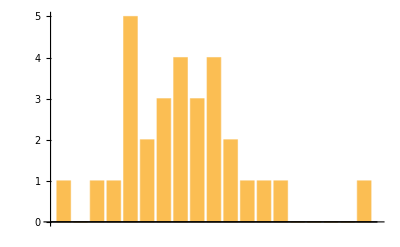

```mathematica
BarChart[enzymtable[[2;;,3]]]
```

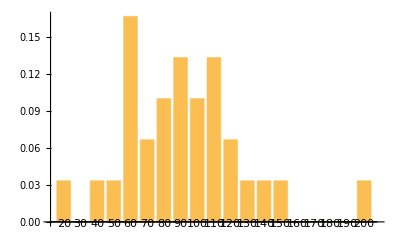

```mathematica
BarChart[enzymtable[[2;;,4]], ChartLabels->enzymtable[[2;;,1]]]
```

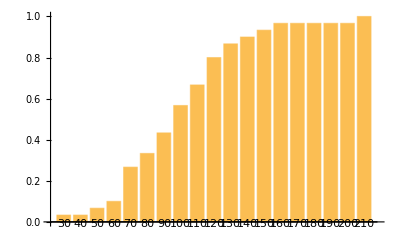

```mathematica
BarChart[enzymtable[[2;;,6]], ChartLabels->enzymtable[[2;;,2]]]
```

We now look at the Histogram function with default options:

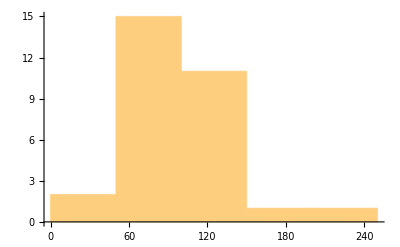

```mathematica
Histogram[enzyme]
```

```mathematica
Histogram[enzyme[[2;;]]]
```

-Graphics-

We now specify the number of bins we would like:

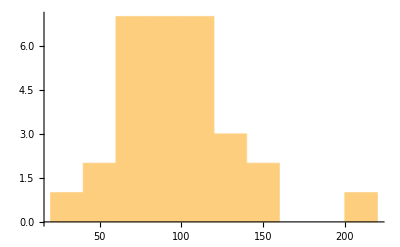

```mathematica
Histogram[enzyme[[2;;]],10]
```

We can also specify range covered by the bins and their width as follows:

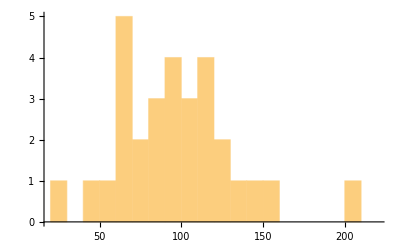

```mathematica
Histogram[enzyme[[2;;]],{20,220,10}]
```

If we select the option “Probability”, we get the relative frequency:

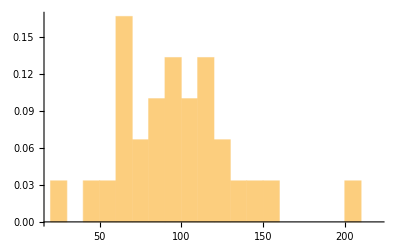

```mathematica
Histogram[enzyme[[2;;]],{20,220,10},"Probability"]
```

If we select the option “PDF”, we get the density (PDF means probability density function):

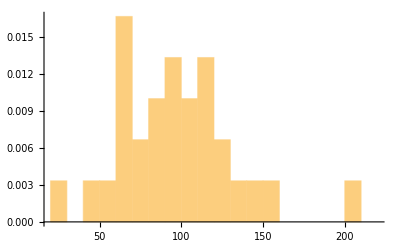

```mathematica
Histogram[enzyme[[2;;]],{20,220,10},"PDF"]
```

If we select the option “CDF”, we get the cumulative relative frequency (CDF means cumulative distribution function):

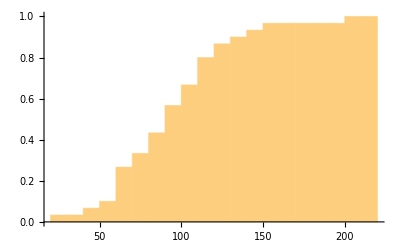

```mathematica
Histogram[enzyme[[2;;]],{20,220,10},"CDF"]
```

We can also get the cumulative count:

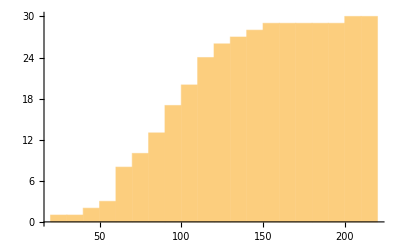

```mathematica
Histogram[enzyme[[2;;]],{20,220,10},"CumulativeCount"]
```

## Measures of central tendency and dispersion

```mathematica
enzyme
```

{Enzyme Concentration(mg/cc),121,25,83,110,60,101,95,81,123,67,113,78,85,145,100,70,93,118,119,57,64,151,48,92,62,104,139,201,68,95}

```mathematica
N[Mean[enzyme[[2;;]]]]
```

95.6

```mathematica
Median[enzyme[[2;;]]]
```

94

Let’s understand how the median has been calculated:

```mathematica
Sort[enzyme[[2;;]]]
```

{25,48,57,60,62,64,67,68,70,78,81,83,85,92,93,95,95,100,101,104,110,113,118,119,121,123,139,145,151,201}

```mathematica
Length[enzyme[[2;;]]]
```

30

```mathematica
Sort[enzyme[[2;;]]][[15;;16]]
```

{93,95}

The mode is calculated as follows:

```mathematica
Commonest[enzyme]
```

{95}

The quartiles are obtained as follows:

```mathematica
Quartiles[enzyme[[2;;]]]
```

{68,94,118}

We can generate a box plot as follows:

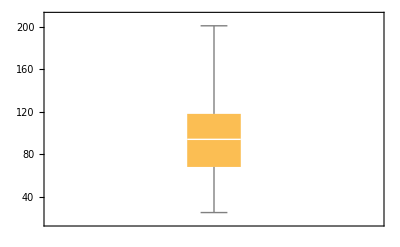

```mathematica
BoxWhiskerChart[enzyme[[2;;]]]
```

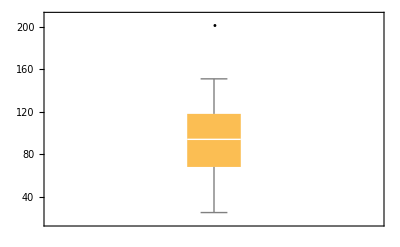

```mathematica
BoxWhiskerChart[enzyme[[2;;]],"Outliers"]
```

```mathematica
(*upper fence is the maximum excluding outlier.*)
```

```mathematica
1.5*InterquartileRange[enzyme[[2;;]]]+Quartiles[enzyme[[2;;]]][[3]]
```

193.

```mathematica
(*we see that the maximum value 201 in the dataset is classified as outlier because it is larger than 193*)
```

We now import the Geyser data:

```mathematica
geyser=Import["geyser.dat"]
```

{{Duration,InterruptionTime},{4.4,78},{3.9,74},{4,68},{4,76},{3.5,80},{4.1,84},{2.3,50},{4.7,93},{1.7,55},{4.9,76},{1.7,58},{4.6,74},{3.4,75},{4.3,80},{1.7,56},{3.9,80},{3.7,69},{3.1,57},{4,90},{1.8,42},{4.1,91},{1.8,51},{3.2,79},{1.9,53},{4.6,82},{2,51},{4.5,76},{3.9,82},{4.3,84},{2.3,53},{3.8,86},{1.9,51},{4.6,85},{1.8,45},{4.7,88},{1.8,51},{4.6,80},{1.9,49},{3.5,82},{4,75},{3.7,73},{3.7,67},{4.3,68},{3.6,86},{3.8,72},{3.8,75},{3.8,75},{2.5,66},{4.5,84},{4.1,70},{3.7,79},{3.8,60},{3.4,86},{4,71},{2.3,67},{4.4,81},{4.1,76},{4.3,83},{3.3,76},{2,55},{4.3,73},{2.9,56},{4.6,83},{1.9,57},{3.6,71},{3.7,72},{3.7,77},{1.8,55},{4.6,75},{3.5,73},{4,70},{3.7,83},{1.7,50},{4.6,95},{1.7,51},{4,82},{1.8,54},{4.4,83},{1.9,51},{4.6,80},{2.9,78},{3.5,81},{2,53},{4.3,89},{1.8,44},{4.1,78},{1.8,61},{4.7,73},{4.2,75},{3.9,73},{4.3,76},{1.8,55},{4.5,86},{2,48},{4.2,77},{4.4,73},{4.1,70},{4.1,88},{4,75},{4.1,83},{2.7,61},{4.6,78},{1.9,61},{4.5,81},{2,51},{4.8,80},{4.1,79},{4.1,82},{4.2,80},{4.5,76},{1.9,56},{4.7,82},{2,47},{4.7,76},{2.5,61},{4.3,75},{4.4,72},{4.4,74},{4.3,69},{4.6,78},{2.1,52},{4.8,91},{4.1,66},{4,71},{4,75},{4.4,81},{4.1,77},{4.3,74},{4,70},{3.9,83},{3.2,53},{4.5,82},{2.2,62},{4.7,73},{4.6,84},{2.2,58},{4.8,82},{4.3,77},{3.8,75},{4,77},{4.1,77},{1.8,53},{4.4,75},{4,78},{2.2,51},{5.1,81},{1.9,52},{5,76},{4.4,73},{4.5,84},{3.8,72},{4.3,89},{4.4,75},{2.2,57},{4.8,81},{1.9,49},{4.7,87},{1.8,43},{4.8,94},{2,45},{4.4,81},{2.5,59},{4.3,82},{4.4,80},{1.9,54},{4.7,75},{4.3,73},{2.2,57},{4.7,80},{2.3,51},{4.6,77},{3.3,66},{4.2,77},{2.9,60},{4.6,86},{3.3,62},{4.2,75},{2.6,67},{4.6,69},{3.7,84},{1.8,58},{4.7,90},{4.5,82},{4.5,71},{4.8,80},{2,51},{4.8,80},{1.9,62},{4.7,84},{2,51},{5.1,81},{4.3,83},{4.8,84},{3,72},{2.1,54},{4.6,75},{4,74},{2.2,51},{5.1,91},{2.9,60},{4.3,80},{2.1,54},{4.7,80},{4.5,70},{1.7,60},{4.2,86},{4.3,78},{1.7,51},{4.4,83},{4.2,76},{2.2,51},{4.7,90},{4,71},{1.8,49},{4.7,88},{1.8,52},{4.5,79},{2.1,61},{4.2,81},{2.1,48},{5.2,84},{2,63}}

```mathematica
Dimensions[geyser]
```

{223,2}

```mathematica
N[Variance[geyser[[2;;]]]]
```

{1.17495,163.819}

```mathematica
StandardDeviation[geyser[[2;;]]]
```

{1.08395,√(4018642/24531)}

```mathematica
N[Sqrt[Variance[geyser[[2;;]]]]]
```

{1.08395,12.7992}

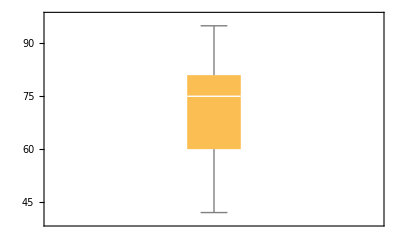

```mathematica
BoxWhiskerChart[ geyser[[2;;,2]]]
```

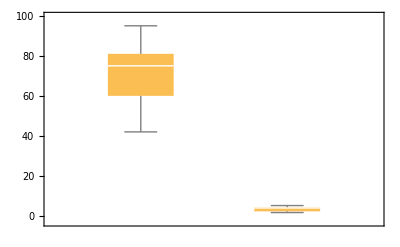

```mathematica
BoxWhiskerChart[ {geyser[[2;;,2]],geyser[[2;;,1]]}]
```

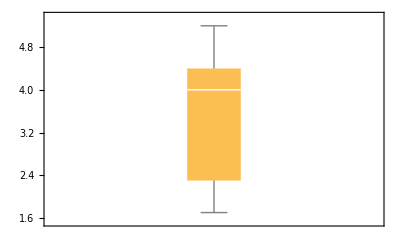
{-Graphics-,-Graphics-}

```mathematica
{BoxWhiskerChart[ geyser[[2;;,1]]],BoxWhiskerChart[ geyser[[2;;,2]]]}
```

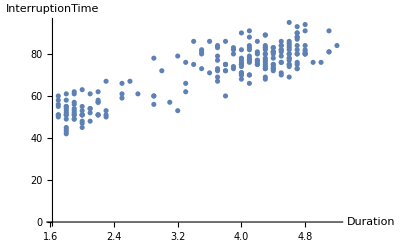

```mathematica
ListPlot[geyser[[2;;]],AxesLabel->geyser[[1]]]
```

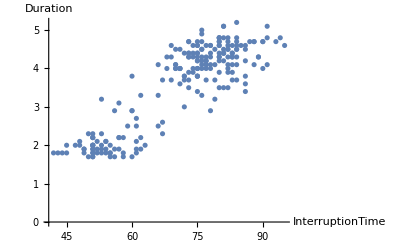

```mathematica
ListPlot[Reverse[geyser[[2;;]],2],AxesLabel-> Reverse[geyser[[1]]]  ]
```